## Box Function

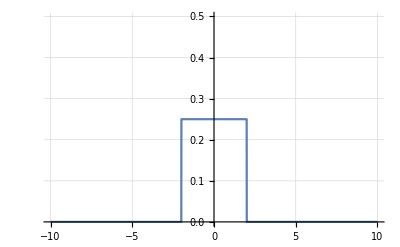

```mathematica
f[x_]:=0.25/;-2<=x<=2;
f[x_]:=0/;x>=2;
f[x_]:=0/;x<=-2;
Plot[f[x],{x,-10,10},PlotRange->{{-10,10},{0,0.5}},GridLines->Automatic]
```

```mathematica
Export[NotebookDirectory[]<>"Box.dat",Table[{ω,f[ω]},{ω,-4,4,0.01}]]
```

\\Client\H$\Documents\acnotes\mbook\box\Box.dat

## Transform to Imaginary time

```mathematica
G[τ_,β_]:=NIntegrate[f[ω]Exp[-τ ω]/(1+Exp[-β ω]),{ω,-Infinity,Infinity}]
β=50.;
Ntau=1000;
```

```mathematica
TabulatedG=Table[{β/Ntau*n,G[β/Ntau*n,β]},{n,0,Ntau}];
Export[NotebookDirectory[]<>"BoxTime.dat",TabulatedG]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {1.99429}. NIntegrate obtained 0.499822 and 0.000647549 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {1.99429}. NIntegrate obtained 0.47566 and 0.000620382 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in ω near {ω} = {1.99429}. NIntegrate obtained 0.453044 and 0.0005958 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

\\Client\H$\Documents\acnotes\mbook\box\BoxTime.dat

## Transform to Matsubara Frequency

```mathematica
nmax=1000
```

1000

```mathematica
iωntable=Table[I(2n+1)π/β,{n,1,nmax}];
```

```mathematica
Giωntable=Table[NIntegrate[TripleCurve[ω]/(iωntable[[j]]-ω),{ω,-Infinity,Infinity}],{j,1,nmax}];
```

```mathematica
ωnReGiωntable=Table[{Im[iωntable[[j]]],Re[Giωntable[[j]]]},{j,1,nmax}];
ωnImGiωntable=Table[{Im[iωntable[[j]]],Im[Giωntable[[j]]]},{j,1,nmax}];
```

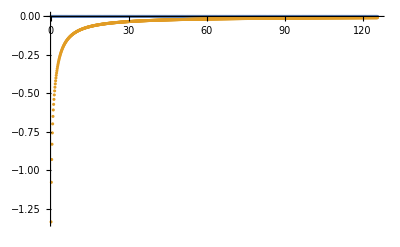

```mathematica
ListPlot[{ωnReGiωntable,ωnImGiωntable},PlotRange->All]
```

```mathematica
Export[NotebookDirectory[]<>"TripleGaussianFrequency.dat",ωnImGiωntable]
```

\\Client\C$\Users\tchen\Documents\acnotes\mbook\imaginary\TripleGaussianFrequency.dat

```mathematica
"/Users/tchen/Documents/acnotes/mbook/b50/TripleGaussianFrequency.dat"
```

/Users/tchen/Documents/acnotes/mbook/b50/TripleGaussianFrequency.dat